{{ψ→InterpolatingFunction[{{0., 10.}, {…, -12., 12., …}}, <>]}}

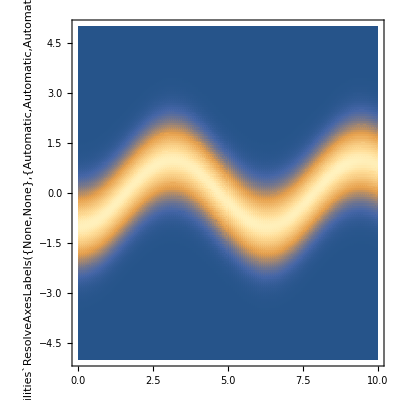

-Graphics-

-Graphics-

```mathematica
ћ=1;
m=1;
ω=1;
u=1;
ψ0=((m*ω)/(ћ*π))^(1/4)ⅇ^(-(m*ω)/(2ћ)(x+u)^2);
s=NDSolve[{I*ћ*D[ψ[t,x],t]==-(ћ^2)/(2m)*D[ψ[t,x],x,x]+((m/2)ω^2)x^2*ψ[t,x],ψ[t,-12]==ψ[t,12],ψ[0,x]==ψ0},ψ,{t,0,10},{x,-12,12}]

DensityPlot[Abs[ψ[t,x]]^2/.s,{t,0,10},{x,-5,5},PlotPoints->150]
DensityPlot[Abs[Re[ψ[t,x]]]/.s,{t,0,10},{x,-5,5},PlotPoints->150]
DensityPlot[Abs[Im[ψ[t,x]]]/.s,{t,0,10},{x,-5,5},PlotPoints->150]
```